```mathematica
Solve[xdd1+ m/M xdd2 + ω^2 x1 ==0, xdd2]
```

{{xdd2→-(M (xdd1+x1 ω^2))/m}}

```mathematica
Solve[xdd2 + m/M xdd1 + ω^2 x2 == 0, xdd1]
```

{{xdd1→-(M (xdd2+x2 ω^2))/m}}

```mathematica
FactorTerms[-(M (xdd2+x2 ω^2))/m+ m/M xdd2 + ω^2 x1 ,{xdd1,x1,x2}]
```

(m xdd2)/M-(M xdd2)/m+x1 ω^2-(M x2 ω^2)/m

```mathematica
Solve[(m xdd2)/M-(M xdd2)/m+x1 ω^2-(M x2 ω^2)/m==0,xdd2]
```

{{xdd2→(M (-m x1 ω^2+M x2 ω^2))/(m^2-M^2)}}

```mathematica
FactorTerms[-(M (xdd1+x1 ω^2))/m + m/M xdd1 + ω^2 x2 ,{xdd1,x1,x2}]
```

(m xdd1)/M-(M xdd1)/m-(M x1 ω^2)/m+x2 ω^2

```mathematica
Solve[(m xdd1)/M-(M xdd1)/m-(M x1 ω^2)/m+x2 ω^2==0,xdd1]
```

{{xdd1→(M (M x1 ω^2-m x2 ω^2))/(m^2-M^2)}}

```mathematica
A={{M^2, -M m}, {-M m, M^2}}
```

{{M^2,-m M},{-m M,M^2}}

```mathematica
Eigenvalues[A]
```

{M (-m+M),M (m+M)}

```mathematica
D[Cos[θ1 - θ2], θ1]
```

-Sin[θ1-θ2]

```mathematica
D[Cos[θ1 - θ2], θ2]
```

Sin[θ1-θ2]

```mathematica
Quit
```

```mathematica
L = 1/2(m1 + m2) l1^2 θd1^2+1/2 m2 l2^2 θd2^2+ m2 l1 l2 Cos[θ1 - θ2] θd1 θd2 + g (m1 + m2) l1 Cos[θ1] + g m2 l2 Cos[θ2]
```

1/2 l1^2 (m1+m2) θd1^2+1/2 l2^2 m2 θd2^2+g l1 (m1+m2) Cos[θ1]+l1 l2 m2 θd1 θd2 Cos[θ1-θ2]+g l2 m2 Cos[θ2]

```mathematica
D[L, θ1]
```

-g l1 (m1+m2) Sin[θ1]-l1 l2 m2 θd1 θd2 Sin[θ1-θ2]

```mathematica
D[L, θ2]
```

l1 l2 m2 θd1 θd2 Sin[θ1-θ2]-g l2 m2 Sin[θ2]

```mathematica
D[D[L, θ1],θ1]
```

-g l1 (m1+m2) Cos[θ1]-l1 l2 m2 θd1 θd2 Cos[θ1-θ2]

```mathematica
D[D[L, θ2],θ2]
```

-l1 l2 m2 θd1 θd2 Cos[θ1-θ2]-g l2 m2 Cos[θ2]

```mathematica
D[D[L, θ1],θ2]
```

l1 l2 m2 θd1 θd2 Cos[θ1-θ2]

```mathematica
D[D[L, θ2],θ1]
```

l1 l2 m2 θd1 θd2 Cos[θ1-θ2]

```mathematica
Lf[θ1_, θ2_] := 1/2(m1 + m2) l1^2 θd1^2+1/2 m2 l2^2 θd2^2+ m2 l1 l2 Cos[θ1 - θ2] θd1 θd2 + g (m1 + m2) l1 Cos[θ1] + g m2 l2 Cos[θ2]
```

```mathematica
Lf[0,0]+D1f[0,0] + D2f[0,0]
```

g l2 m2+g l1 (m1+m2)+1/2 l1^2 (m1+m2) θd1^2+l1 l2 m2 θd1 θd2+1/2 l2^2 m2 θd2^2+2 ∂_0 ∂_0 (g l2 m2+g l1 (m1+m2)+1/2 l1^2 (m1+m2) θd1^2+l1 l2 m2 θd1 θd2+1/2 l2^2 m2 θd2^2)

```mathematica
Series[L, {θ1,0,2},{θ2,0,2}]
```

((g l2 m2+g l1 (m1+m2)+1/2 l1^2 (m1+m2) θd1^2+l1 l2 m2 θd1 θd2+1/2 l2^2 m2 θd2^2)+(-1/2 g l2 m2-1/2 l1 l2 m2 θd1 θd2) θ2^2+O[θ2]^3)+(l1 l2 m2 θd1 θd2 θ2+O[θ2]^3) θ1+((-1/2 g l1 (m1+m2)-1/2 l1 l2 m2 θd1 θd2)+1/4 l1 l2 m2 θd1 θd2 θ2^2+O[θ2]^3) θ1^2+O[θ1]^3

```mathematica
Simplify[g l2 m2+g l1 (m1+m2)+1/2 l1^2 (m1+m2) θd1^2+l1 l2 m2 θd1 θd2+1/2 l2^2 m2 θd2^2+(-1/2 g l2 m2-1/2 l1 l2 m2 θd1 θd2) θ2^2+l1 l2 m2 θd1 θd2 θ2 θ1 + -1/2 g l1 (m1+m2)-1/2 l1 l2 m2 θd1 θd2]
```

1/2 (g l1 (m1+m2)-g l2 m2 (-2+θ2^2)+l1^2 (m1+m2) θd1^2+l1 l2 m2 (1+2 θ1 θ2-θ2^2) θd1 θd2+l2^2 m2 θd2^2)

```mathematica
Solve[(m1 + m2)l1^2 θdd1 + m2 l1 l2 θdd2 + g(m1 + m2) l1 θ1 == 0, θdd2]
```

{{θdd2→(-g m1 θ1-g m2 θ1-l1 m1 θdd1-l1 m2 θdd1)/(l2 m2)}}

```mathematica
Solve[m2 l1 l2 θdd1 + m2 l2^2 θdd2 + g m2 l2 θ2 == 0, θdd1]
```

{{θdd1→(-g θ2-l2 θdd2)/l1}}

```mathematica
FactorTerms[(m1 + m2)l1^2 ((-g θ2-l2 θdd2)/l1) + m2 l1 l2 θdd2 + g(m1 + m2) l1 θ1, {θdd2, θ1, θ2}]
```

-l1 (-g m1 θ1-g m2 θ1+g m1 θ2+g m2 θ2+l2 m1 θdd2)

```mathematica
Simplify[-l1 (-g m1 θ1-g m2 θ1+g m1 θ2+g m2 θ2+l2 m1 θdd2)==-l1 l2 m1 θdd2 + g(m1 + m2) l1 θ1 - g(m1 + m2)l1  θ2]
```

True

```mathematica
FactorTerms[m2 l1 l2 θdd1 + m2 l2^2((-g m1 θ1-g m2 θ1-l1 m1 θdd1-l1 m2 θdd1)/(l2 m2)) + g m2 l2 θ2, {θdd2, θ1, θ2}]
```

-l2 (g m1 θ1+g m2 θ1-g m2 θ2+l1 m1 θdd1)

```mathematica
Simplify[-l2 (g m1 θ1+g m2 θ1-g m2 θ2+l1 m1 θdd1) == -m1 l1 l2 θdd1 - g l2(m1 + m2) θ1 + g m2 l2 θ2]
```

True

```mathematica
Solve[{(m1 + m2)l1^2 θdd1 + m2 l1 l2 θdd2 + g(m1 + m2) l1 θ1 == 0,m2 l1 l2 θdd1 + m2 l2^2 θdd2 + g m2 l2 θ2 == 0}, {θdd1, θdd2}]
```

{{θdd1→-(g m1 θ1+g m2 θ1-g m2 θ2)/(l1 m1),θdd2→-(-g m1 θ1-g m2 θ1+g m1 θ2+g m2 θ2)/(l2 m1)}}

```mathematica
gA=({{-(g m1 +g m2)/(l1 m1), -(-g m2)/(l1 m1)}, {-(-g m1 -g m2)/(l2 m1), -(g m1 +g m2)/(l2 m1)}})
```

{{-(g m1+g m2)/(l1 m1),(g m2)/(l1 m1)},{-(-g m1-g m2)/(l2 m1),-(g m1+g m2)/(l2 m1)}}

```mathematica
Eigenvalues[gA]
```

{1/(2 l1^2 l2^2 m1^4)g (-l1^2 l2 m1^4-l1 l2^2 m1^4-l1^2 l2 m1^3 m2-l1 l2^2 m1^3 m2-√((l1^2 l2 m1^4+l1 l2^2 m1^4+l1^2 l2 m1^3 m2+l1 l2^2 m1^3 m2)^2-4 (l1^3 l2^3 m1^8+l1^3 l2^3 m1^7 m2))),1/(2 l1^2 l2^2 m1^4)g (-l1^2 l2 m1^4-l1 l2^2 m1^4-l1^2 l2 m1^3 m2-l1 l2^2 m1^3 m2+√((l1^2 l2 m1^4+l1 l2^2 m1^4+l1^2 l2 m1^3 m2+l1 l2^2 m1^3 m2)^2-4 (l1^3 l2^3 m1^8+l1^3 l2^3 m1^7 m2)))}

```mathematica
A=({{l2, -m2 l2 /(m1 + m2)}, {-l1, l1}})
```

{{l2,-(l2 m2)/(m1+m2)},{-l1,l1}}

```mathematica
FullSimplify[Eigenvalues[A]]
```

{1/2 (l1+l2-(√((l1-l2)^2 m1+(l1+l2)^2 m2))/(√(m1+m2))),1/2 (l1+l2+(√((l1-l2)^2 m1+(l1+l2)^2 m2))/(√(m1+m2)))}

```mathematica
Simplify[1/2 (l1+l2-(√((l1-l2)^2 m1+(l1+l2)^2 m2))/(√(m1+m2)))==1/2(l1 + l2 - Sqrt[(l1 + l2)^2 - (4 m1 l1 l2)/(m1 + m2)])]
```

(-√((l1-l2)^2 m1+(l1+l2)^2 m2)+√(m1+m2) √((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))/(√(m1+m2))==0

```mathematica
Det[A - λ{{1, 0}, {0, 1}}]
```

l1 l2-(l1 l2 m2)/(m1+m2)-l1 λ-l2 λ+λ^2

```mathematica
FullSimplify[Solve[l1 l2-(l1 l2 m2)/(m1+m2)-l1 λ-l2 λ+λ^2==0, λ]]
```

{{λ→1/2 (l1+l2-√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))},{λ→1/2 (l1+l2+√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))}}

```mathematica
FullSimplify[-g(m1 + m2)/(m1 l1 l2)1/2 (l1+l2-√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2))), Assumptions->{m1 == m2, l1 == l2}]
```

(g (-2 l2+√2 √(l2^2)))/l2^2

```mathematica
FullSimplify[-g(m1 + m2)/(m1 l1 l2)1/2 (l1+l2-√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))]
```

-(g (m1+m2) (l1+l2-√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2))))/(2 l1 l2 m1)

```mathematica
FullSimplify[(l1+l2-√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))==4(l1+l2+√((l1+l2)^2-(4 l1 l2 m1)/(m1+m2)))]
```

3 (l1+l2)+5 √((l1+l2)^2-(4 l1 l2 m1)/(m1+m2))==0

```mathematica
FullSimplify[3 (l1+l2)+5 √((l1+l2)^2-(4 l1 l2 m1)/(m1+m2))==0, Assumptions->m1 == m2]
```

3 (l1+l2)+5 √(l1^2+l2^2)==0

```mathematica
Solve[%, l1]
```

{{l1→1/16 (9 l2-5 ⅈ √7 l2)},{l1→1/16 (9 l2+5 ⅈ √7 l2)}}

```mathematica
Plot3D[{(x+y)^2 = 0.32 x y},{x,-1.2,1.2},{y,-1.2,1.2}]
```

-Graphics3D-

```mathematica
FullSimplify[3 (l1+l2)+5 √((l1+l2)^2-(4 l1 l2 m1)/(m1+m2))==0, Assumptions->l1 == l2]
```

3 l2+5 √((l2^2 m2)/(m1+m2))==0

```mathematica
Solve[%,m1]
```

{{m1→(16 m2)/9}}

```mathematica
Acirc=({{2, -1, -1}, {-1, 2, -1}, {-1, -1, 2}})
```

{{2,-1,-1},{-1,2,-1},{-1,-1,2}}

```mathematica
Eigenvalues[Acirc]
```

{3,3,0}

```mathematica
Det[Acirc-({{λ, 0, 0}, {0, λ, 0}, {0, 0, λ}})]
```

-9 λ+6 λ^2-λ^3

```mathematica
Solve[(2-λ)^3-3(2-λ)-2==0,λ]
```

{{λ→0},{λ→3},{λ→3}}

```mathematica
Eigenvectors[Acirc]
```

{{-1,0,1},{-1,1,0},{1,1,1}}

```mathematica
Orthogonalize[%]
```

{{-1/(√2),0,1/(√2)},{-1/(√6),√(2/3),-1/(√6)},{1/(√3),1/(√3),1/(√3)}}

```mathematica
2*%
```

{{-√2,0,√2},{-√(2/3),2 √(2/3),-√(2/3)},{2/(√3),2/(√3),2/(√3)}}

```mathematica
Solve[{2 v1 - v2 - v3 == 3 v1, 2 v2 - v1 - v3 == 3 v2, 2 v3 - v1 - v2 == 3 v3}, {v1, v2, v3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{v3→-v1-v2}}

```mathematica
Adeg=({{1, -ϵ^2}, {-1, 1}})
```

{{1,-ϵ^2},{-1,1}}

```mathematica
Eigenvalues[Adeg]
```

{1-ϵ,1+ϵ}

```mathematica
Eigenvectors[Adeg]
```

{{ϵ,1},{-ϵ,1}}

```mathematica
Cp = 1; Cm = 1; php=0; phm=0;
```

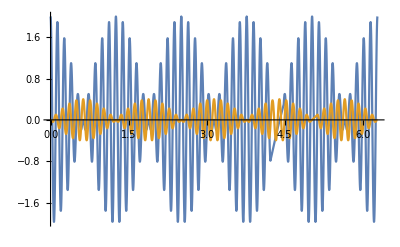

```mathematica
Plot[{Cp Cos[50t + php] +Cm Cos[45t + phm],.2 Cp Cos[50t + php] -.2 Cm Cos[45t + phm]},{t, 0, 2Pi}]
```

```mathematica
Simplify[Cos[(om + ep)t]-Cos[om t]]
```

-Cos[om t]+Cos[(ep+om) t]

```mathematica
newA=ω0^2/(m^2 - M^2)({{M^2, -Mm}, {-Mm, M^2}})
```

{{(M^2 ω0^2)/(m^2-M^2),-(Mm ω0^2)/(m^2-M^2)},{-(Mm ω0^2)/(m^2-M^2),(M^2 ω0^2)/(m^2-M^2)}}

```mathematica
Eigenvalues[newA]
```

{((-M^2-Mm) ω0^2)/(-m^2+M^2),((-M^2+Mm) ω0^2)/(-m^2+M^2)}

```mathematica
FullSimplify[%]
```

```mathematica
{((M^2+Mm) ω0^2)/(m^2-M^2),((M^2-Mm) ω0^2)/(m^2-M^2)}
```

```mathematica
Solve[{x1dd + m/M x2dd + w0^2 x1 == 0, x2dd + m/M x1dd + w0^2 x2 == 0}, {x1dd, x2dd}]
```

{{x1dd→-(M (M w0^2 x1-m w0^2 x2))/(-m^2+M^2),x2dd→-(m M w0^2 x1-M^2 w0^2 x2)/(m^2-M^2)}}

```mathematica
Expand[1/(1-m^2/M^2)]
```

1/(1-m^2/M^2)

```mathematica
Augh=({{-(M (M w0^2))/(-m^2+M^2), -(M (-m w0^2))/(-m^2+M^2)}, {-(m M w0^2)/(m^2-M^2), -(-M^2 w0^2)/(m^2-M^2)}})
```

{{-(M^2 w0^2)/(-m^2+M^2),(m M w0^2)/(-m^2+M^2)},{-(m M w0^2)/(m^2-M^2),(M^2 w0^2)/(m^2-M^2)}}

```mathematica
Eigenvalues[Augh]
```

{((-m-M) M w0^2)/(-m^2+M^2),((m-M) M w0^2)/(-m^2+M^2)}

```mathematica
Simplify[%]
```

{(M w0^2)/(m-M),-(M w0^2)/(m+M)}

```mathematica
Simplify[(M^2 + M m)/(M^2 - m^2)]
```

-M/(m-M)

```mathematica
Simplify[(M^2 - M m)/(M^2 - m^2)]
```

M/(m+M)